```mathematica
Haoran:  why is my mean and Yvar sometimes complex?

This code examines the mean ,variance and covariance of a very large swarm of robots as they  move inside a circular workplace.
The swarm is large, but the robots are small in comparison, and together cover an area of constant volume A.
 When they are pushed to a side, they flow like water.
We want to know the mean position variance and covariance of this swarm
```

```mathematica
THe circular area has radius 1, The area under a chord at height h
```

### Area = -(1-h)√((2-h) h)+ArcCos[1-h]

```mathematica
cor(X,Y) = (cov(X,Y))/(sd(X)*sd(Y))
```

```mathematica
Clear[x,h,y]
```

```mathematica
Assuming[0< h< 2, FullSimplify[∫_(1-h)^1 ∫_(-√(1-x^2))^(√(1-x^2)) ⅆyⅆx]]
```

-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h]

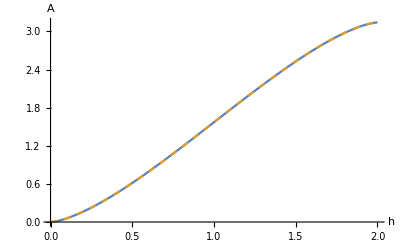

```mathematica
Plot[{ -(1-h)√((2-h) h)+ArcCos[1-h],-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h]},{h,0,2},PlotStyle->{Automatic,Dashed},AxesLabel->{"h","A"}]
```

### Xmean = -(2 ((-2+h) h)^(3/2))/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]))

```mathematica
Assuming[0<h<2, FullSimplify[(∫_(1-h)^1 ∫_(-√(1-x^2))^(√(1-x^2)) xⅆyⅆx)/(-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h])]]
```

ConditionalExpression[-(2 ((-2+h) h)^(3/2))/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])),h<1]

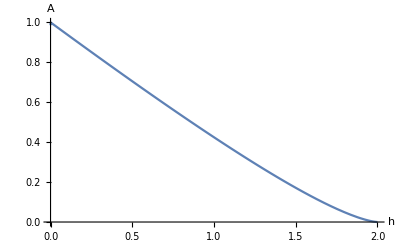

```mathematica
Plot[-(2 ((-2+h) h)^(3/2))/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])),{h,0,2},AxesLabel->{"h","A"}]
```

### Ymean = 0

```mathematica
Assuming[0<h<2, FullSimplify[(∫_(1-h)^1 ∫_(-√(1-x^2))^(√(1-x^2)) yⅆyⅆx)/(-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h])]]
```

0

### Xvar = (64 (-2+h)^3 h^3+9 ((-1+h) √(-(-2+h) h)+ArcCos[1-h]) (4 ArcCos[1-h]+Sin[4 ArcSin[1-h]]))/(144 ((-1+h) √(-(-2+h) h)+ArcCos[1-h])^2)

```mathematica
Assuming[0<h<2, FullSimplify[(∫_(1-h)^1 ∫_(-√(1-x^2))^(√(1-x^2)) x^2 ⅆyⅆx)/(-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h])]]
```

ConditionalExpression[(-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h])/(4 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])),h<1]

```mathematica
Assuming[0<h<2, FullSimplify[-(-(2 ((-2+h) h)^(3/2))/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])))^2]]
```

```mathematica
FullSimplify[(-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h])/(4 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]))-(4 (-2+h)^3 h^3)/(9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2)]
```

(-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h]))/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2)

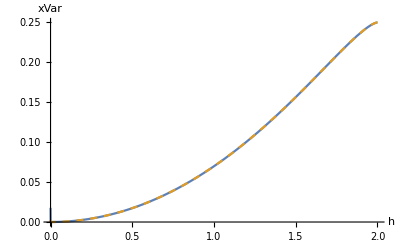

```mathematica
Plot[{(-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h]))/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2),(64 (-2+h)^3 h^3+9 ((-1+h) √(-(-2+h) h)+ArcCos[1-h]) (4 ArcCos[1-h]+Sin[4 ArcSin[1-h]]))/(144 ((-1+h) √(-(-2+h) h)+ArcCos[1-h])^2)},{h,0,2},AxesLabel->{"h","xVar"},PlotStyle->{Automatic,Dashed}]
```

### Yvar = (12 ArcCos[1-h]-8 Sin[2 ArcCos[1-h]]+Sin[4 ArcCos[1-h]])/(48 ((-1+h) √(-(-2+h) h)+ArcCos[1-h]))

```mathematica
Assuming[0<h<2, FullSimplify[(∫_(1-h)^1 ∫_(-√(1-x^2))^(√(1-x^2)) y^2 ⅆyⅆx)/(-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h])-(0)^2]]
```

(ⅈ (ⅈ √(-(-2+h) h) (3+h (1+2 (-3+h) h))-3 ArcCosh[1-h]))/(12 (-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h]))

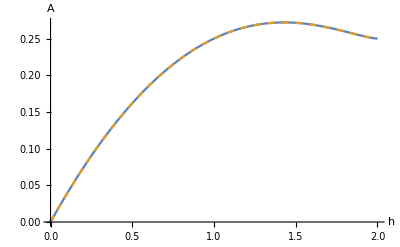

```mathematica
Plot[{(ⅈ (ⅈ √(-(-2+h) h) (3+h (1+2 (-3+h) h))-3 ArcCosh[1-h]))/(12 (-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h])),(12 ArcCos[1-h]-8 Sin[2 ArcCos[1-h]]+Sin[4 ArcCos[1-h]])/(48 ((-1+h) √(-(-2+h) h)+ArcCos[1-h]))},{h,0,2},AxesLabel->{"h","A"},PlotStyle->{Automatic,Dashed}]
```

### Covariance(X,Y) = E[X Y]- E[X]E[Y] = E[X Y]- E[X] 0 =E[X Y] = 0

```mathematica
Assuming[0<h<2, FullSimplify[(∫_(1-h)^1 ∫_(-√(1-x^2))^(√(1-x^2)) x yⅆyⅆx)/(-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h])]]
```

0

```mathematica
{{(h (5-2 h^2) √(1-h^2)+3 π-3 ArcCos[h])/(6 (2 h √(1-h^2)+π+2 ArcSin[h])),0},{0,(16 (-1+h^2)^3+9 (h √(1-h^2)+π-ArcCos[h]) (h √(1-h^2) (-1+2 h^2)+π-ArcCos[h]))/(36 (h √(1-h^2)+π-ArcCos[h])^2)}}//MatrixForm
```

((h (5-2 h^2) √(1-h^2)+3 π-3 ArcCos[h])/(6 (2 h √(1-h^2)+π+2 ArcSin[h])) | 0
0 | (16 (-1+h^2)^3+9 (h √(1-h^2)+π-ArcCos[h]) (h √(1-h^2) (-1+2 h^2)+π-ArcCos[h]))/(36 (h √(1-h^2)+π-ArcCos[h])^2))

### Correlation(X,Y) = E[X Y]- E[X]E[Y] = E[X Y]- E[X] 0 =E[X Y] = 0

```mathematica
Assuming[0<h<2, FullSimplify[(∫_(1-h)^1 ∫_(-√(1-x^2))^(√(1-x^2)) x yⅆyⅆx)/(-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h])]]
```

0

### Rotate Correlation Matrix

```mathematica
FullSimplify[RotationMatrix[β].({{a, 0}, {0, c}}).RotationMatrix[β]ᵀ]//MatrixForm
```

(a Cos[β]^2+c Sin[β]^2 | (a-c) Cos[β] Sin[β]
(a-c) Cos[β] Sin[β] | c Cos[β]^2+a Sin[β]^2)

```mathematica
RotationMatrix[β]//MatrixForm
RotationMatrix[β]ᵀ//MatrixForm
{{(-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h]))/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2),0},{0,(ⅈ (ⅈ √(-(-2+h) h) (3+h (1+2 (-3+h) h))-3 ArcCosh[1-h]))/(12 (-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h]))}}//MatrixForm
```

(Cos[β] | -Sin[β]
Sin[β] | Cos[β])

(Cos[β] | Sin[β]
-Sin[β] | Cos[β])

((-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h]))/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2) | 0
0 | (ⅈ (ⅈ √((2-h) h) (3+h (1+2 (-3+h) h))-3 ArcCosh[1-h]))/(12 (-√((2-h) h)+√((2-h) h^3)+ArcCos[1-h])))

```mathematica
RotationMatrix[β].{{(-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h]))/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2),0},{0,(ⅈ (ⅈ √(-(-2+h) h) (3+h (1+2 (-3+h) h))-3 ArcCosh[1-h]))/(12 (-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h]))}}
```

```mathematica
Assuming[-1<h<1, FullSimplify[{{((-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h])) Cos[β])/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2),-(ⅈ (ⅈ √((2-h) h) (3+h (1+2 (-3+h) h))-3 ArcCosh[1-h]) Sin[β])/(12 (-√((2-h) h)+√((2-h) h^3)+ArcCos[1-h]))},{((-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h])) Sin[β])/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2),(ⅈ (ⅈ √((2-h) h) (3+h (1+2 (-3+h) h))-3 ArcCosh[1-h]) Cos[β])/(12 (-√((2-h) h)+√((2-h) h^3)+ArcCos[1-h]))}}]]
```

```mathematica
{{((-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h])) Cos[β])/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2),((√(-(-2+h) h) (3+h (1+2 (-3+h) h))+3 ⅈ ArcCosh[1-h]) Sin[β])/(12 (-√(-(-2+h) h)+√(-(-2+h) h^3)+ArcCos[1-h]))},{((-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h])) Sin[β])/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2),-((√(-(-2+h) h) (3+h (1+2 (-3+h) h))+3 ⅈ ArcCosh[1-h]) Cos[β])/(12 (-√(-(-2+h) h)+√(-(-2+h) h^3)+ArcCos[1-h]))}}//MatrixForm
```

(((-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h])) Cos[β])/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2) | ((√((2-h) h) (3+h (1+2 (-3+h) h))+3 ⅈ ArcCosh[1-h]) Sin[β])/(12 (-√((2-h) h)+√((2-h) h^3)+ArcCos[1-h]))
((-16 (-2+h)^3 h^3+9 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]) (-√((-2+h) h)+√(-2+h) h^(3/2) (5+2 (-3+h) h)+ArcCosh[1-h])) Sin[β])/(36 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])^2) | -((√((2-h) h) (3+h (1+2 (-3+h) h))+3 ⅈ ArcCosh[1-h]) Cos[β])/(12 (-√((2-h) h)+√((2-h) h^3)+ArcCos[1-h])))

```mathematica
Assuming[-1<h<1, FullSimplify[Covxy[β,h]/(√(Varx[β,h]*Vary[β,h]))]]
```

$Aborted

### Calcs (contains initialization cell that must run before the demonstration can)

```mathematica
(RotationMatrix[β].{-(2 ((-2+h) h)^(3/2))/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])),0})⟦1⟧
(RotationMatrix[β].{-(2 ((-2+h) h)^(3/2))/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h])),0})⟦2⟧
```

-(2 ((-2+h) h)^(3/2) Cos[β])/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]))

-(2 ((-2+h) h)^(3/2) Sin[β])/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]))

```mathematica
Meanx[0,1/2]
```

(ⅈ √3)/(4 (-(ⅈ √3)/4+(ⅈ π)/3))

```mathematica
FindMaximum[{Varx[π/2,h],h>0&&h<2},h]
```

{0.271943,{h→1.42914}}

```mathematica
Maximize[{Varx[π/2,h],h>0&&h<2},h]
```

$Aborted

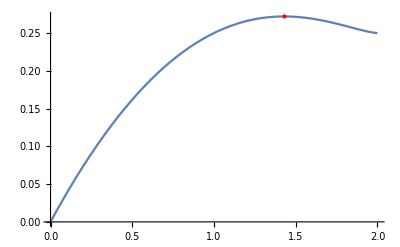

```mathematica
Plot[Varx[π/2,h],{h,0,2},Epilog->{Red,PointSize[Large],Point[{1.4291422537777079,0.27194269409487615}]}]
```

{0.090776,{h→0.917085}}

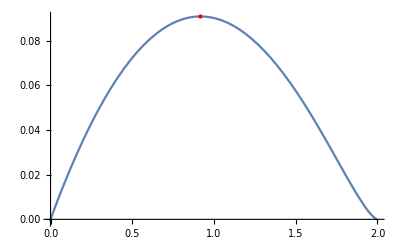

```mathematica
FindMaximum[{Covxy[3π/4,h],h>0&&h<2},h]
Plot[Covxy[3π/4,h],{h,0,2},Epilog->{Red,PointSize[Large],Point[{0.9170848796751496,0.0907759942557099}]}]
```

```mathematica
Meanx[β_,h_]:=(2 ((2-h) h)^(3/2) Cos[β])/(3 ((-1+h) √((2-h) h)+ArcCos[1-h]))
Meany[β_,h_]:=(2 ((2-h) h)^(3/2) Sin[β])/(3 ((-1+h) √((2-h) h)+ArcCos[1-h]))
(* FullSimplify[RotationMatrix[β].({{a, 0}, {0, c}}).RotationMatrix[β]ᵀ]//MatrixForm
({{a Cos[β]^2+c Sin[β]^2, (a-c) Cos[β] Sin[β]}, {(a-c) Cos[β] Sin[β], c Cos[β]^2+a Sin[β]^2}})*)
VarXh[h_]:=(64 (-2+h)^3 h^3+9 ((-1+h) √(-(-2+h) h)+ArcCos[1-h]) (4 ArcCos[1-h]+Sin[4 ArcSin[1-h]]))/(144 ((-1+h) √(-(-2+h) h)+ArcCos[1-h])^2);
VarYh[h_]:=(12 ArcCos[1-h]-8 Sin[2 ArcCos[1-h]]+Sin[4 ArcCos[1-h]])/(48 ((-1+h) √(-(-2+h) h)+ArcCos[1-h]))
Varx[β_,h_]:=VarXh[h] Cos[β]^2+VarYh[h] Sin[β]^2
Vary[β_,h_]:=VarYh[h] Cos[β]^2+VarXh[h] Sin[β]^2
Covxy[β_,h_]:=(VarXh[h]-VarYh[h]) Cos[β] Sin[β]
Corxy[β_,h_]:=Covxy[β,h]/(√(Varx[β,h]*Vary[β,h]))
numPts = 20;
swarmPtsS = Flatten[Table[1/numPts{+i+Boole[EvenQ[j]] 1/2,+j√3/2},{i,-numPts,numPts},{j,-Round[2/√3 numPts],Round[2/√3 numPts]}],1];
swarmPts=Select[swarmPtsS,((#⟦1⟧)^2+(#⟦2⟧)^2)<1&];
```

### Plot

```mathematica
Manipulate[
 Module[{x,y,mean,cov,bwid=0.05,varx,vary,padding,imsize=220},
x=Chop[Meanx[β,h]];
y=Chop[Meany[β,h]];
mean={x,y};
cov=Chop[Covxy[β,h]];
varx =Chop[ Varx[β,h]];
vary =  Chop[Vary[β,h]];
padding={{30,6},{3,20}};
Row[{Column[{
(*Mean*)Plot[{{Meanx[β,h],Meany[β,h]}},{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","mean"},PlotLegends-> Placed[{Row[{"mean ",Style["x",Italic]}],Row[{"mean ",Style["y",Italic]}]},{.65,0.85}], ImageSize->imsize,Exclusions->None,ImagePadding->padding,AxesOrigin->{0,0},
PlotRange->{{0,2π},{-1,1}},PlotPoints->ControlActive[9,Automatic],
PlotStyle->{ColorData[97,"ColorList"]⟦1⟧,ColorData[97,"ColorList"]⟦2⟧}, Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦1⟧,Point[{β,x}],ColorData[97,"ColorList"]⟦2⟧,Point[{β,y}]}],
(*correlation*)Plot[{Corxy[β,h]},{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","correlation"}, ImageSize->imsize,Exclusions->None,ImagePadding->padding,
PlotRange->{{0,2π},1.1{-1,1}},PlotPoints->ControlActive[9,Automatic],
PlotStyle->{ColorData[97,"ColorList"]⟦6⟧},Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦6⟧,Point[{β,Corxy[β,h]}]} ],
(*covariance*)Plot[{Covxy[β,h]},{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","covariance"}, ImageSize->imsize,Exclusions->None,ImagePadding->padding,PlotPoints->ControlActive[9,Automatic],
PlotRange->{{0,2π},0.1{-1,1}},
PlotStyle->{ColorData[97,"ColorList"]⟦5⟧},Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦5⟧,Point[{β,cov}]} ]
}](*end of column*)
Column[{
Graphics[{
{LightBlue,Disk[{0,0},1](*interior region of square*)},
{White,Rotate[Rectangle[{-1,-1},{1-h,1}],β,{0,0}](*draw the robot region*)},
{Darker[Green],Arrowheads[.04{-1,1}],Arrow[{(1-h){Cos[β],Sin[β]},(1){Cos[β],Sin[β]}}],
Text["h",(1-h/2){Cos[β+π/16],Sin[β+π/16]}]},
{Black,Thickness[bwid],Circle[{0,0},1+bwid](*obstacles*)},
If[showStats,{Black,Text[StringForm["area=``\nmean=``\ncov=``",-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h],Chop[mean],Chop[cov]],{0,1/2}]}], (*optional title info*)
(*draw swarm of robots*)
If[showParticles,{PointSize[0.011],Lighter[Blue,.5],Point[If[h<2,Select[swarmPts,(*half-plane test*)
({Cos[β],Sin[β]}.(#-(1-h){Cos[β],Sin[β]})>0)&],swarmPts]]}],
(*draw the mean path*)
{ColorData[97,"ColorList"]⟦1⟧,Thick, Circle[{0,0},-(2 ((-2+h) h)^(3/2))/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]))]},
(*draw the direction of the vector*)
{Blue,Thickness[.01],Arrow[{{0,0},1/2{Cos[β],Sin[β]}}]},
(*draw the mean*)
{ColorData[97,"ColorList"]⟦2⟧,PointSize[Large],Point[mean]},
(*draw the covariance ellipse*)
{ColorData[97,"ColorList"]⟦3⟧,Opacity[0],EdgeForm[{Thick,Red}],Ellipsoid[mean,4{{varx, cov},{cov,vary}}]}
},ImageSize->300,PlotRange->7/6{{-1,1},{-1,1}},PlotRangeClipping->True],
(*variance*)Plot[{{Vary[β,h],Varx[β,h]}},{β,0,2π},
Ticks->{{0,π/2,π,3π/2, 2π},Automatic},AxesLabel->{"β","variance"},
PlotLegends->{Row[{"var ",Style["y",Italic]}],Row[{"var ",Style["x",Italic]}]},
PlotRange->{{0,2π},{0,0.3}},PlotPoints->ControlActive[9,Automatic],
 ImageSize->190,Exclusions->None,PlotStyle->{ColorData[97,"ColorList"]⟦3⟧,ColorData[97,"ColorList"]⟦4⟧}, Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦4⟧,Point[{β,varx}],ColorData[97,"ColorList"]⟦3⟧,Point[{β,vary}]}]}]
}]],
Row[{Control@{{β,0,"β"},0,6.28,0.01, Appearance->"Labeled",ImageSize->Small},Spacer[10],Control@{{h,0.5,"h"},0.001,2,0.001, Appearance->"Labeled",ImageSize->Small},Spacer[10],Control@{{showParticles,False,"show particles"},{True,False}},Spacer[10],Control@{{showStats,False,"show values"},{True,False}}}]
,SaveDefinitions->True]
```

Plot for paper

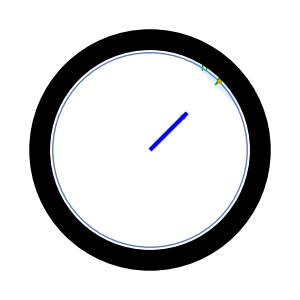
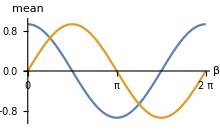
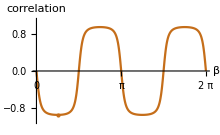
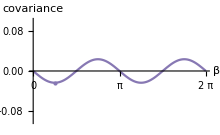

```mathematica
Module[{x,y,mean,cov,bwid=0.05,varx,vary,padding,imsize=220,h = 1/8,β=π/4,showStats=False,showParticles=False},
x=Chop[Meanx[β,h]];
y=Chop[Meany[β,h]];
mean={x,y};
cov=Chop[Covxy[β,h]];
varx =Chop[ Varx[β,h]];
vary =  Chop[Vary[β,h]];
padding={{30,6},{3,20}};
Row[{
Graphics[{
{LightBlue,Disk[{0,0},1](*interior region of square*)},
{White,Rotate[Rectangle[{-1,-1},{1-h,1}],β,{0,0}](*draw the robot region*)},
{Darker[Green],Arrowheads[.04{-1,1}],Arrow[{(1-h){Cos[β],Sin[β]},(1){Cos[β],Sin[β]}}],
Text["h",(1-h/2){Cos[β+π/16],Sin[β+π/16]}]},
{Black,Thickness[bwid],Circle[{0,0},1+bwid](*obstacles*)},
If[showStats,{Black,Text[StringForm["area=``\nmean=``\ncov=``",-√((2-h) h)+√(-(-2+h) h^3)+ArcCos[1-h],Chop[mean],Chop[cov]],{0,1/2}]}], (*optional title info*)
(*draw swarm of robots*)
If[showParticles,{PointSize[0.011],Lighter[Blue,.5],Point[If[h<2,Select[swarmPts,(*half-plane test*)
({Cos[β],Sin[β]}.(#-(1-h){Cos[β],Sin[β]})>0)&],swarmPts]]}],
(*draw the mean path*)
{ColorData[97,"ColorList"]⟦1⟧,Thick, Circle[{0,0},-(2 ((-2+h) h)^(3/2))/(3 (√(-2+h) h^(3/2)-√((-2+h) h)+ArcCosh[1-h]))]},
(*draw the direction of the vector*)
{Blue,Thickness[.01],Arrow[{{0,0},1/2{Cos[β],Sin[β]}}]},
(*draw the mean*)
{ColorData[97,"ColorList"]⟦2⟧,PointSize[Large],Point[mean]},
(*draw the covariance ellipse*)
{ColorData[97,"ColorList"]⟦3⟧,Opacity[0],EdgeForm[{Thick,Red}],Ellipsoid[mean,4{{varx, cov},{cov,vary}}]}
},ImageSize->300,PlotRange->7/6{{-1,1},{-1,1}},PlotRangeClipping->True],
(*Mean*)Plot[{{Meanx[β,h],Meany[β,h]}},{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","mean"},PlotLegends-> Placed[{Row[{"mean ",Style["x",Italic]}],Row[{"mean ",Style["y",Italic]}]},{.65,0.85}], ImageSize->imsize,Exclusions->None,ImagePadding->padding,AxesOrigin->{0,0},
PlotRange->{{0,2π},{-1,1}},PlotPoints->ControlActive[9,Automatic],
PlotStyle->{ColorData[97,"ColorList"]⟦1⟧,ColorData[97,"ColorList"]⟦2⟧}, Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦1⟧,Point[{β,x}],ColorData[97,"ColorList"]⟦2⟧,Point[{β,y}]}],
(*correlation*)Plot[{Corxy[β,h]},{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","correlation"}, ImageSize->imsize,Exclusions->None,ImagePadding->padding,
PlotRange->{{0,2π},1.1{-1,1}},PlotPoints->ControlActive[9,Automatic],
PlotStyle->{ColorData[97,"ColorList"]⟦6⟧},Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦6⟧,Point[{β,Corxy[β,h]}]} ],
(*covariance*)Plot[{Covxy[β,h]},{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","covariance"}, ImageSize->imsize,Exclusions->None,ImagePadding->padding,PlotPoints->ControlActive[9,Automatic],
PlotRange->{{0,2π},0.1{-1,1}},
PlotStyle->{ColorData[97,"ColorList"]⟦5⟧},Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦5⟧,Point[{β,cov}]} ]
}]
]
```

Plot for paper

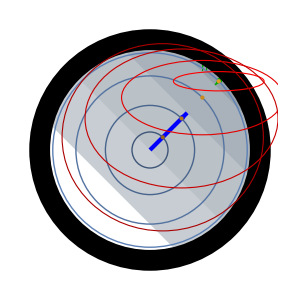

```mathematica
Module[{xv,yv,βv ,x,y,mean,cov,covv,varyv,varxv,bwid=0.05,varx,vary,padding,imsize=220,h = 1/8,β=π/4,showStats=False,showParticles=False},
hv = {1/8,1/2,1,3/2};
x=Chop[Meanx[β,h]];
y=Chop[Meany[β,h]];
mean={x,y};
cov=Chop[Covxy[β,h]];
varx =Chop[ Varx[β,h]];
vary =  Chop[Vary[β,h]];

xv=Table[Chop[Meanx[β,hv⟦i⟧]],{i,Length[hv]}];
yv=Table[Chop[Meany[β,hv⟦i⟧]],{i,Length[hv]}];
covv=Table[Chop[Covxy[β,hv⟦i⟧]],{i,Length[hv]}];
varxv=Table[Chop[Varx[β,hv⟦i⟧]],{i,Length[hv]}];
varyv=Table[Chop[Vary[β,hv⟦i⟧]],{i,Length[hv]}];
 padding={{30,6},{3,20}};
Row[{
Graphics[{
{Darker[LightBlue],Disk[{0,0},1](*interior region of square*)},
Table[{White,Opacity[0.2],Rotate[Rectangle[{-1,-1},{1-hv⟦i⟧,1}],β,{0,0}](*draw the robot region*)},{i,Length@hv}],
{White,Rotate[Rectangle[{-1,-1},{1-hv⟦Length@hv⟧,1}],β,{0,0}](*draw the robot region*)},
{Darker[Green],Arrowheads[.04{-1,1}],Arrow[{(1-h){Cos[β],Sin[β]},(1){Cos[β],Sin[β]}}],
Text["h",(1-h/2){Cos[β+π/16],Sin[β+π/16]}]},
{Black,Thickness[bwid],Circle[{0,0},1+bwid](*obstacles*)},
(*draw the mean path*)
Table[
{Darker[ColorData[97,"ColorList"]⟦1⟧,(i-1)/(Length[hv]+5)],Thick, Circle[{0,0},-(2 ((-2+hv⟦i⟧) hv⟦i⟧)^(3/2))/(3 (√(-2+hv⟦i⟧) hv⟦i⟧^(3/2)-√((-2+hv⟦i⟧) hv⟦i⟧)+ArcCosh[1-hv⟦i⟧]))]},{i,Length[hv]}],
(*draw the direction of the vector*)
{Blue,Thickness[.01],Arrow[{{0,0},1/2{Cos[β],Sin[β]}}]},
(*draw the mean*)
Table[{Darker[ColorData[97,"ColorList"]⟦2⟧,(i-1)/(Length[hv]+5)],PointSize[Large],Point[{xv⟦i⟧,xv⟦i⟧}]},{i,Length[hv]}],
(*draw the covariance ellipse*)
Table[{EdgeForm[{Dashed,Thick,Darker[Red,(i-1)/(Length[hv]+5)]}],Opacity[0],Ellipsoid[{xv⟦i⟧,xv⟦i⟧},4{{varxv⟦i⟧, covv⟦i⟧},{covv⟦i⟧,varyv⟦i⟧}}]},{i,Length[hv]}]
},ImageSize->300,PlotRange->7/6{{-1,1},{-1,1}},PlotRangeClipping->True]
}]
]
```

```mathematica
hv = {1/8,1/2,1,3/2};
Table[Darker[ColorData[97,"ColorList"]⟦1⟧,(i-1)/(Length[hv]+5)],{i,Length[hv]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ColorData[97,"ColorList"]⟦3⟧
```

-Graphics-

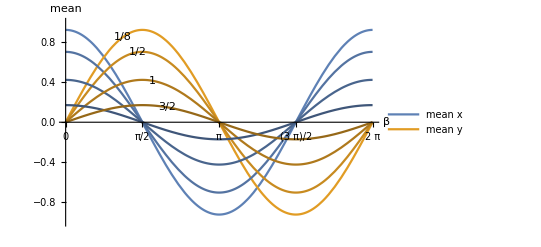

```mathematica
(*Mean*)
h = 1/8;β=π/4;
padding={{30,6},{3,20}};
imsize=220;
x=Chop[Meanx[β,h]];
y=Chop[Meany[β,h]];
hv = {1/8,1/2,1,3/2};
βv =1.2*Range[0,Length@hv]/Length@hv +π/2-.4;
Plot[{{Meanx[β,hv⟦1⟧],Meany[β,hv⟦1⟧],Meanx[β,hv⟦2⟧],Meany[β,hv⟦2⟧],Meanx[β,hv⟦3⟧],Meany[β,hv⟦3⟧],Meanx[β,hv⟦4⟧],Meany[β,hv⟦4⟧]}},{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","mean"},PlotLegends-> Placed[{Row[{"mean ",Style["x",Italic]}],Row[{"mean ",Style["y",Italic]}]},{.65,0.85}], Exclusions->None,ImagePadding->padding,AxesOrigin->{0,0},
PlotRange->{{0,2π},{-1,1}},PlotPoints->ControlActive[9,Automatic],
PlotStyle->Flatten[Table[{Darker[ColorData[97,"ColorList"]⟦1⟧,(i-1)/(Length[hv]+5)],Darker[ColorData[97,"ColorList"]⟦2⟧,(i-1)/(Length[hv]+5)]},{i,Length[hv]}]],Epilog-> Table[Text[Style[hv⟦i⟧],{βv⟦i⟧,Meany[βv⟦i⟧,hv⟦i⟧]},Background->Directive[{Opacity[0.8],White}]],{i,Length@hv}]
(*Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦1⟧,Point[{β,x}],ColorData[97,"ColorList"]⟦2⟧,Point[{β,y}]}*)]
```

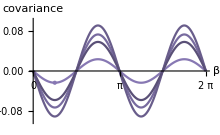

```mathematica
(*covariance*)
(*Mean*)
h = 1/8;β=π/4;
padding={{30,6},{3,20}};
imsize=220;
x=Chop[Meanx[β,h]];
y=Chop[Meany[β,h]];
hv = {1/8,1/2,1,3/2};
Plot[{{Covxy[β,hv⟦1⟧],Covxy[β,hv⟦2⟧],Covxy[β,hv⟦3⟧],Covxy[β,hv⟦4⟧]}},{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","covariance"},
ImageSize->imsize,Exclusions->None,ImagePadding->padding,AxesOrigin->{0,0},
PlotRange->{{0,2π},0.1{-1,1}},PlotPoints->ControlActive[9,Automatic],
PlotStyle->Table[Darker[ColorData[97,"ColorList"]⟦5⟧,(i-1)/(Length[hv]+5)],{i,Length[hv]}],Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦1⟧,Point[{β,x}],ColorData[97,"ColorList"]⟦5⟧,Point[{β,Covxy[β,hv⟦1⟧]}]}]
(*max covariance at h=1*)
```

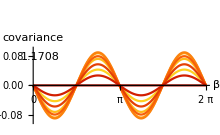

```mathematica
(*covariance*)
(*Mean*)
h = 1/8;β=π/4;
padding={{30,6},{3,20}};
imsize=220;
x=Chop[Meanx[β,h]];
y=Chop[Meany[β,h]];
hv = Table[i,{i,0.25,2,0.25}];
Plot[Table[Covxy[β,hv⟦i⟧],{i,Length[hv]}],{β,0,2π},Ticks->{{0,π/2,π,3π/2, 2π},Automatic}, AxesLabel->{"β","covariance"},PlotStyle->ColorData["SolarColors"]/@(Reverse[Range[0,Length@hv]]/Length@hv),
ImageSize->imsize,Exclusions->None,ImagePadding->padding,AxesOrigin->{0,0},
PlotRange->{{0,2π},0.1{-1,1}},PlotPoints->ControlActive[9,Automatic],Evaluated->True,(*Epilog->{PointSize[Large],ColorData[97,"ColorList"]⟦1⟧,Point[{β,x}],ColorData[97,"ColorList"]⟦5⟧,Point[{β,Covxy[β,hv⟦1⟧]}]},*)
Epilog-> Table[Text[Style[βv⟦i⟧],{hv⟦i⟧,Varx[βv⟦i⟧,hv⟦i⟧]},Background->Directive[{Opacity[0.8],White}]],{i,1,Length@βv,4}]
]
(*max covariance at β=1 & π/4*)
```

```mathematica
Table[i,{i,0.25,2,0.25}]
```

{0.25,0.5,0.75,1.,1.25,1.5,1.75,2.}

```mathematica
Reverse[Range[0,Length@hv]]
```

{8,7,6,5,4,3,2,1,0}

```mathematica
Range[1,4,0.2]
```

{1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.}

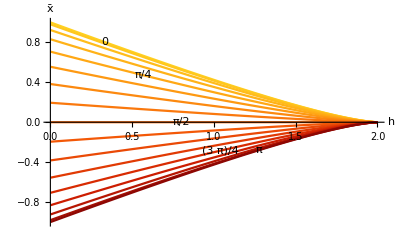

```mathematica
(*Mean*)
h = 1/8;β=π/4;
padding={{30,6},{3,20}};
imsize=220;
x=Chop[Meanx[β,h]];
y=Chop[Meany[β,h]];
βv=Range[0,π,π/16];
Clear[h]
hv = 1*Range[0,Length@βv]/Length@βv +1/3;
Plot[Evaluate[Table[Meanx[βv⟦i⟧,h],{i,Length@βv}]],{h,0.001,2},AxesLabel->{"h","x̄"},PlotStyle->ColorData["SolarColors"]/@(Reverse[Range[0,Length@βv]]/Length@βv),Epilog-> Table[Text[Style[βv⟦i⟧],{hv⟦i⟧,Meanx[βv⟦i⟧,hv⟦i⟧]},Background->Directive[{Opacity[0.8],White}]],{i,1,Length@βv,4}]]
(*max mean at h=0*)
```

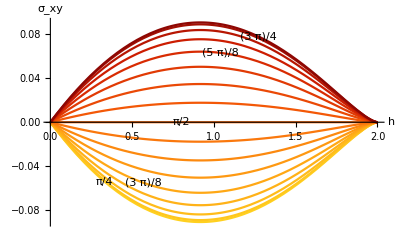

```mathematica
(*covariance*)
h = 1/8;β=π/4;
padding={{30,6},{3,20}};
imsize=220;
x=Chop[Meanx[β,h]];
y=Chop[Meany[β,h]];
βv=Range[π/4,3π/4,π/32];
Clear[h]
hv = 1*Range[0,Length@βv]/Length@βv +1/3;
Plot[Evaluate[Table[Covxy[βv⟦i⟧,h],{i,Length@βv}]],{h,0.001,2},AxesLabel->{"h","σ_xy"},PlotStyle->ColorData["SolarColors"]/@(Reverse[Range[0,Length@βv]]/Length@βv),Epilog-> Table[Text[Style[βv⟦i⟧],{hv⟦i⟧,Covxy[βv⟦i⟧,hv⟦i⟧]},Background->Directive[{Opacity[0.8],White}]],{i,1,Length@βv,4}]]
(*max covariance at h=1*)
```

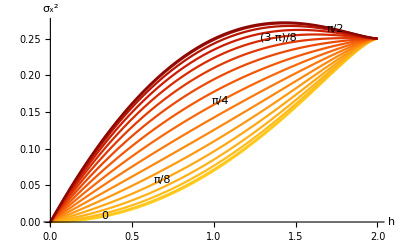

```mathematica
βv= Range[0,π/2,π/32];
hv = 1.5*Range[0,Length@βv]/Length@βv +1/3;
Clear[h];
Plot[Evaluate[Table[Varx[βv⟦i⟧,h],{i,Length@βv}]],{h,0.001,2},AxesLabel->{"h","σ_x^2"},PlotStyle->ColorData["SolarColors"]/@(Reverse[Range[0,Length@βv]]/Length@βv),Epilog-> Table[Text[Style[βv⟦i⟧],{hv⟦i⟧,Varx[βv⟦i⟧,hv⟦i⟧]},Background->Directive[{Opacity[0.8],White}]],{i,1,Length@βv,4}]]
```

```mathematica
Covxy[3π/4,0]
```

0

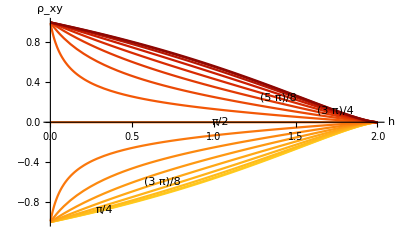

```mathematica
βv=Range[π/4,3π/4,π/32];
hv = 1.5*Range[0,Length@βv]/Length@βv +1/3;
Clear[h]
Plot[Evaluate[Table[Corxy[βv⟦i⟧,h],{i,Length@βv}]],{h,0.001,2},AxesLabel->{"h","ρ_xy"},PlotStyle->ColorData["SolarColors"]/@(Reverse[Range[0,Length@βv]]/Length@βv),Epilog-> Table[Text[Style[βv⟦i⟧],{hv⟦i⟧,Corxy[βv⟦i⟧,hv⟦i⟧]},Background->Directive[{Opacity[0.8],White}]],{i,1,Length@βv,4}]]
```

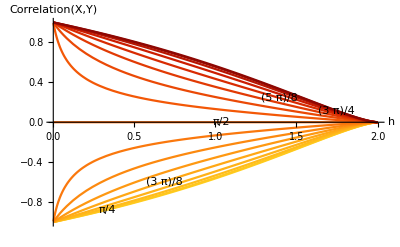

```mathematica
βv=Range[π/4,3π/4,π/32];
hv = 1.5*Range[0,Length@βv]/Length@βv +1/3;
Clear[h]
Plot[Evaluate[Table[Corxy[βv⟦i⟧,h],{i,Length@βv}]],{h,0.001,2},AxesLabel->{"h","Correlation(X,Y)"},PlotStyle->ColorData["SolarColors"]/@(Reverse[Range[0,Length@βv]]/Length@βv),Epilog-> Table[Text[Style[βv⟦i⟧],{hv⟦i⟧,Corxy[βv⟦i⟧,hv⟦i⟧]},Background->Directive[{Opacity[0.8],White}]],{i,1,Length@βv,4}]]
```